## Appendix 1

Code for problem 1

```mathematica
(* Question 1 *)
```

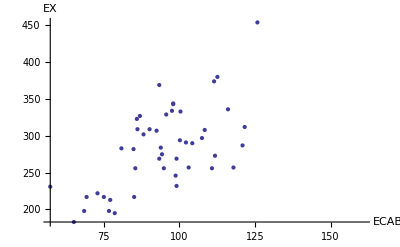
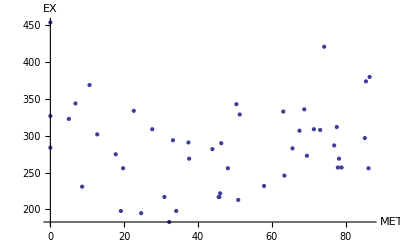
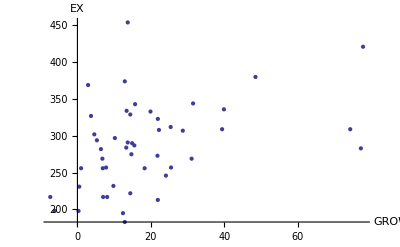
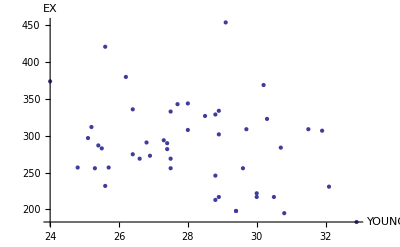
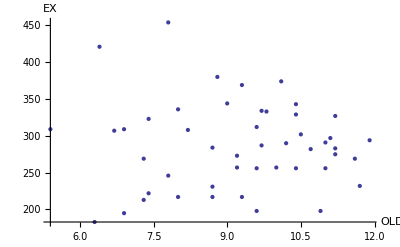
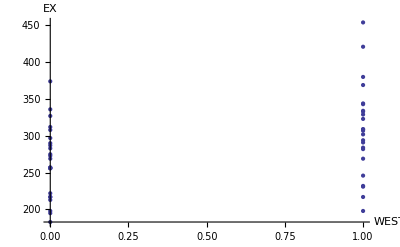

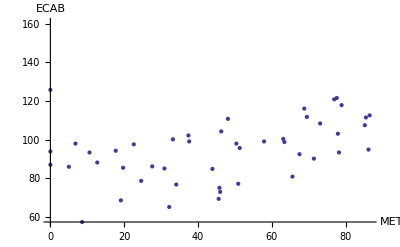
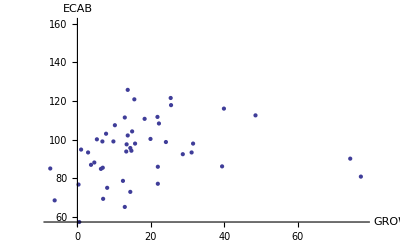

```mathematica
(*Heres the original data, each grouping is a different state*)
data=  {{256,85.50,19.7,6.90,29.6,11.0,0},{275,94.30,17.7,14.7,26.4,11.2,0},
	  {327,87.00,0.00,3.70,28.5,11.2,0},{297,107.5,85.2,10.2,25.1,11.1,0},
	  {256,94.90,86.2,1.00,25.3,10.4,0},{312,121.6,77.6,25.4,25.2,9.60,0},
	  {374,111.5,85.5,12.9,24.0,10.1,0},{257,117.9,78.9,25.5,24.8,9.20,0},
	  {257,103.1,77.9,7.80,25.7,10.0,0},{336,116.1,68.8,39.9,26.4,8.00,0},
	  {269,93.40,78.2,31.1,27.5,7.30,0},{213,77.20,50.9,21.9,28.8,7.30,0},
	  {308,108.4,73.1,22.2,28.0,8.20,0},{273,111.8,69.5,21.8,26.9,9.20,0},
	  {256,110.8,48.1,18.3,27.5,9.60,0},{287,120.9,76.9,15.5,25.4,9.70,0},
	  {290,104.3,46.3,14.9,27.4,10.2,0},{217,85.10,30.9,-7.4,30.0,9.30,0},
	  {198,76.80,34.1,0.30,29.4,9.60,0},{217,75.10,45.8,8.10,28.9,8.70,0},
	  {195,78.70,24.6,12.4,30.8,6.90,0},{183,65.20,32.2,12.9,32.9,6.30,0},
	  {222,73.00,46.0,14.4,30.0,7.40,0},{283,80.90,65.6,77.2,25.5,11.2,0},
	  {217,69.40,45.6,7.00,30.5,8.00,1},{231,57.40,8.60,0.50,32.1,8.70,1},
	  {329,95.70,51.3,14.4,28.8,10.4,1},{294,100.2,33.2,5.30,27.3,11.9,1},
	  {232,99.10,57.9,9.80,25.6,11.7,1},{369,93.40,10.6,2.90,30.2,9.30,1},
	  {302,88.20,12.7,4.60,28.9,10.5,1},{269,99.10,37.6,6.80,26.6,11.6,1},
	  {291,102.2,37.4,13.7,26.8,11.0,1},{323,86.00,5.00,21.9,30.3,7.40,1},
	  {198,68.60,19.1,-6.2,29.4,10.9,1},{282,84.90,43.9,6.40,27.4,10.7,1},
	  {246,98.80,63.4,24.1,28.8,7.80,1},{309,86.20,27.6,39.4,31.5,5.40,1},
	  {309,90.20,71.4,74.3,29.7,6.90,1},{334,97.60,22.6,13.4,28.9,9.70,1},
	  {284,93.90,0.00,13.3,30.7,8.70,1},{454,125.8,0.00,13.7,29.1,7.80,1},
	  {344,98.00,6.80,31.5,28.0,9.00,1},{307,92.50,67.5,28.7,31.9,6.70,1},
	  {333,100.4,63.1,19.9,27.5,9.80,1},{343,98.00,50.4,15.7,27.7,10.4,1},
	  {421,205.0,74.2,77.8,25.6,6.40,1},{380,112.6,86.5,48.5,26.2,8.80,1}};

(*Separating the data into individual lists*)
EX=Transpose[data][[1]];
ECAB=Transpose[data][[2]];
MET=Transpose[data][[3]];
GROW=Transpose[data][[4]];
YOUNG=Transpose[data][[5]];
OLD=Transpose[data][[6]];
WEST=Transpose[data][[7]];

(*Simple plots of the data.  Fist is all of the independent variables on one plot*)
ListPlot[{ECAB,MET,GROW,YOUNG,OLD,WEST}, PlotLegends->{"ECAB","MET","GROW","YOUNG","OLD","WEST STATE"},PlotStyle->{Red,Blue,Green,Orange,Purple,Yellow},Mesh->Full,InterpolationOrder->2,Joined->True];

(*each individual independent var plotted against the dependent var.*)
{ListPlot[{EX,ECAB},PlotLegends->{"EX","ECAB"},PlotStyle->{Magenta,Red},InterpolationOrder->2,Joined->True],
ListPlot[{EX,MET},PlotLegends->{"EX","MET"},PlotStyle->{Magenta,Blue},InterpolationOrder->2,Joined->True],
ListPlot[{EX,GROW},PlotLegends->{"EX","ECAB"},PlotStyle->{Magenta,Green},InterpolationOrder->2,Joined->True],
ListPlot[{EX,YOUNG},PlotLegends->{"EX","ECAB"},PlotStyle->{Magenta,Orange},InterpolationOrder->2,Joined->True],
ListPlot[{EX,OLD},PlotLegends->{"EX","ECAB"},PlotStyle->{Magenta,Purple},InterpolationOrder->2,Joined->True],
ListPlot[{EX,WEST},PlotLegends->{"EX","ECAB"},PlotStyle->{Magenta,Yellow},InterpolationOrder->2,Joined->True]};

(*Scatter plots of independent variables against the dependent variable*)
{ListPlot[Transpose[{ECAB,EX}],AxesLabel->{"ECAB","EX"}],
ListPlot[Transpose[{MET,EX}],AxesLabel->{"MET","EX"}],
ListPlot[Transpose[{GROW,EX}],AxesLabel->{"GROW","EX"}],
ListPlot[Transpose[{YOUNG,EX}],AxesLabel->{"YOUNG","EX"}],
ListPlot[Transpose[{OLD,EX}],AxesLabel->{"OLD","EX"}],
ListPlot[Transpose[{WEST,EX}],AxesLabel->{"WEST","EX"}]}

(*Scatter plots of independent variables against other independent variables*)
{ListPlot[Transpose[{MET,ECAB}],AxesLabel->{"MET","ECAB"}],
ListPlot[Transpose[{GROW,ECAB}],AxesLabel->{"GROW","ECAB"}],
ListPlot[Transpose[{YOUNG,ECAB}],AxesLabel->{"YOUNG","ECAB"}],
ListPlot[Transpose[{OLD,ECAB}],AxesLabel->{"OLD","ECAB"}],
ListPlot[Transpose[{GROW,MET}],AxesLabel->{"GROW","MET"}],
ListPlot[Transpose[{YOUNG,MET}],AxesLabel->{"YOUNG","MET"}],
ListPlot[Transpose[{OLD,MET}],AxesLabel->{"OLD","MET"}],
ListPlot[Transpose[{YOUNG,GROW}],AxesLabel->{"YOUNG","GROW"}],
ListPlot[Transpose[{OLD,MET}],AxesLabel->{"OLD","GROW"}],
ListPlot[Transpose[{OLD,YOUNG}],AxesLabel->{"OLD","YOUNG"}]}
```

```mathematica
(* Question 2 *)
```

```mathematica
ex = Transpose[{ECAB,MET, GROW, YOUNG, OLD, WEST,EX}];
Clear[ecab,met,grow,young,old,west]
lm=LinearModelFit[ex,{ecab,met,grow,young,old,west},{ecab,met,grow,young,old,west}];
Normal[lm]
```

356.182+1.4185 ecab+0.57159 grow-0.660153 met-1.85507 old+35.4723 west-6.67466 young

```mathematica
(* Question 3 *)
```

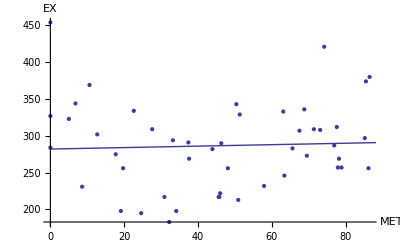

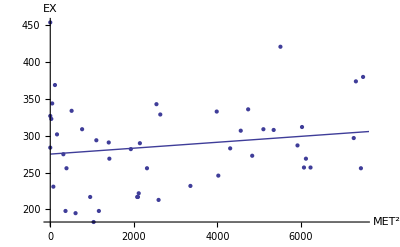

```mathematica
L=Normal[LinearModelFit[Transpose[{MET,EX}],x,x]];
Show[ListPlot[Transpose[{MET,EX}],AxesLabel->{"MET","EX"}],Plot[L,{x,0,100}]]
Clear[x]
L2=Normal[LinearModelFit[Transpose[{MET*MET,EX}],x,x]];
Show[ListPlot[Transpose[{MET*MET,EX}],AxesLabel->{"MET^2","EX"}],Plot[L2,{x,0,8000}]]

(*seems to be constant*)
```

```mathematica
ex2=Transpose[{ECAB,MET,GROW,YOUNG,OLD,WEST,MET*MET,EX}];
Clear[ecab,met,grow,young,old,west,met2]
lm2=LinearModelFit[ex2,{ecab,met,grow,young,old,west,met2},{ecab,met,grow,young,old,west,met2}];
Normal[lm2]
```

119.118+1.39542 ecab+0.695336 grow-3.04214 met+0.030914 met2+4.12078 old+34.0731 west+0.607602 young

```mathematica
(* Question 4 *)
```

```mathematica
lm["ParameterPValues"]
```

{0.251897,0.0020158,0.0683222,0.186155,0.377459,0.796219,0.013701}

```mathematica
ex3=Transpose[{ECAB,MET,GROW,YOUNG,OLD,EX}];
Clear[ecab,met,grow,young,old]
lm3=LinearModelFit[ex3,{ecab,met,grow,young,old},{ecab,met,grow,young,old}];
lm3["ParameterPValues"]
```

{0.825835,0.000140578,0.0661806,0.0526171,0.919921,0.540358}

```mathematica
ex4=Transpose[{ECAB,MET,GROW,YOUNG,EX}];
Clear[ecab,met,grow,young]
lm4=LinearModelFit[ex4,{ecab,met,grow,young},{ecab,met,grow,young}];
lm4["ParameterPValues"]
```

{0.132839,0.0000671046,0.0118255,0.0614497,0.504932}

```mathematica
ex5=Transpose[{MET,GROW,YOUNG,EX}];
Clear[met,grow,young]
lm5=LinearModelFit[ex5,{met,grow,young},{met,grow,young}];
lm5["ParameterPValues"]
Normal[lm5]
```

{9.85785×10^-6,0.0117987,0.000824996,0.00486014}

668.821+1.52654 grow-0.982591 met-12.9968 young

```mathematica
(* Question 5 *)
```

```mathematica
Subscript[SSE, k]=0;
Subscript[SSE, l]=0;
SST=0;
For[i=1,i<49,i++,Subscript[SSE, k]=Subscript[SSE, k]+(EX[[i]]-lm[ECAB[[i]],MET[[i]],GROW[[i]],YOUNG[[i]],OLD[[i]],WEST[[i]]])^2]
For[i=1,i<49,i++,Subscript[SSE, l]=Subscript[SSE, l]+(EX[[i]]-lm3[ECAB[[i]],MET[[i]],GROW[[i]],YOUNG[[i]],OLD[[i]]])^2]
For[i=1,i<49,i++,SST=SST+(EX[[i]]-Mean[EX])^2]
f=((Subscript[SSE, l]-Subscript[SSE, k])/(6-5))/(Subscript[SSE, k]/(48-5-1))
F=((SST-Subscript[SSE, l])/5)/(Subscript[SSE, l]/(48-5-1))
f>F
```

6.79688

9.64732

False

```mathematica
Subscript[SSE, k]=0;
Subscript[SSE, l]=0;
For[i=1,i<49,i++,Subscript[SSE, k]=Subscript[SSE, k]+(EX[[i]]-lm[ECAB[[i]],MET[[i]],GROW[[i]],YOUNG[[i]],OLD[[i]],WEST[[i]]])^2]
For[i=1,i<49,i++,Subscript[SSE, l]=Subscript[SSE, l]+(EX[[i]]-lm4[ECAB[[i]],MET[[i]],GROW[[i]],YOUNG[[i]]])^2]
f=((Subscript[SSE, l]-Subscript[SSE, k])/(6-4))/(Subscript[SSE, k]/(48-4-1))
F=((SST-Subscript[SSE, l])/5)/(Subscript[SSE, l]/(48-5-1))
f>F
```

3.706

9.48504

False

```mathematica
Subscript[SSE, k]=0;
Subscript[SSE, l]=0;
For[i=1,i<49,i++,Subscript[SSE, k]=Subscript[SSE, k]+(EX[[i]]-lm[ECAB[[i]],MET[[i]],GROW[[i]],YOUNG[[i]],OLD[[i]],WEST[[i]]])^2]
For[i=1,i<49,i++,Subscript[SSE, l]=Subscript[SSE, l]+(EX[[i]]-lm5[MET[[i]],GROW[[i]],YOUNG[[i]]])^2]
f=((Subscript[SSE, l]-Subscript[SSE, k])/(6-3))/(Subscript[SSE, k]/(48-3-1))
F=((SST-Subscript[SSE, l])/5)/(Subscript[SSE, l]/(48-5-1))
f>F
```

10.3201

3.90771

True

```mathematica
Normal[lm4]
```

229.906+1.68092 ecab+0.76161 grow-0.830069 met-2.91085 young

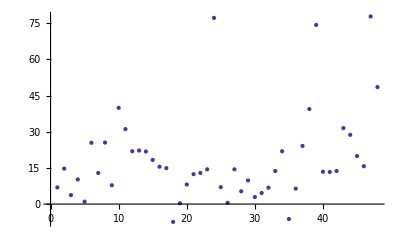

77.2

18.7292

```mathematica
ListPlot[GROW]
GROW[[24]]
Mean[GROW]
```

```mathematica
(*Heres the original data, each grouping is a different state*)
data2=  {{256,85.50,19.7,6.90,29.6,11.0,0},{275,94.30,17.7,14.7,26.4,11.2,0},
	  {327,87.00,0.00,3.70,28.5,11.2,0},{297,107.5,85.2,10.2,25.1,11.1,0},
	  {256,94.90,86.2,1.00,25.3,10.4,0},{312,121.6,77.6,25.4,25.2,9.60,0},
	  {374,111.5,85.5,12.9,24.0,10.1,0},{257,117.9,78.9,25.5,24.8,9.20,0},
	  {257,103.1,77.9,7.80,25.7,10.0,0},{336,116.1,68.8,39.9,26.4,8.00,0},
	  {269,93.40,78.2,31.1,27.5,7.30,0},{213,77.20,50.9,21.9,28.8,7.30,0},
	  {308,108.4,73.1,22.2,28.0,8.20,0},{273,111.8,69.5,21.8,26.9,9.20,0},
	  {256,110.8,48.1,18.3,27.5,9.60,0},{287,120.9,76.9,15.5,25.4,9.70,0},
	  {290,104.3,46.3,14.9,27.4,10.2,0},{217,85.10,30.9,-7.4,30.0,9.30,0},
	  {198,76.80,34.1,0.30,29.4,9.60,0},{217,75.10,45.8,8.10,28.9,8.70,0},
	  {195,78.70,24.6,12.4,30.8,6.90,0},{183,65.20,32.2,12.9,32.9,6.30,0},
	  {222,73.00,46.0,14.4,30.0,7.40,0},
	  {217,69.40,45.6,7.00,30.5,8.00,1},{231,57.40,8.60,0.50,32.1,8.70,1},
	  {329,95.70,51.3,14.4,28.8,10.4,1},{294,100.2,33.2,5.30,27.3,11.9,1},
	  {232,99.10,57.9,9.80,25.6,11.7,1},{369,93.40,10.6,2.90,30.2,9.30,1},
	  {302,88.20,12.7,4.60,28.9,10.5,1},{269,99.10,37.6,6.80,26.6,11.6,1},
	  {291,102.2,37.4,13.7,26.8,11.0,1},{323,86.00,5.00,21.9,30.3,7.40,1},
	  {198,68.60,19.1,-6.2,29.4,10.9,1},{282,84.90,43.9,6.40,27.4,10.7,1},
	  {246,98.80,63.4,24.1,28.8,7.80,1},{309,86.20,27.6,39.4,31.5,5.40,1},
	  {334,97.60,22.6,13.4,28.9,9.70,1},
	  {284,93.90,0.00,13.3,30.7,8.70,1},{454,125.8,0.00,13.7,29.1,7.80,1},
	  {344,98.00,6.80,31.5,28.0,9.00,1},{307,92.50,67.5,28.7,31.9,6.70,1},
	  {333,100.4,63.1,19.9,27.5,9.80,1},{343,98.00,50.4,15.7,27.7,10.4,1},
	  {380,112.6,86.5,48.5,26.2,8.80,1}};
```

```mathematica
EX2=Transpose[data2][[1]];
ECAB2=Transpose[data2][[2]];
MET3=Transpose[data2][[3]];
GROW2=Transpose[data2][[4]];
YOUNG2=Transpose[data2][[5]];
OLD2=Transpose[data2][[6]];
WEST2=Transpose[data2][[7]];
```

```mathematica
ex42=Transpose[{ECAB2,MET3,GROW2,YOUNG2,EX2}];
Clear[ecab,met,grow,young]
lm42=LinearModelFit[ex42,{ecab,met,grow,young},{ecab,met,grow,young}];
Normal[lm42]
```

-17.7251+2.8681 ecab+0.988889 grow-0.885007 met+1.90303 young